```mathematica
mat={{a,b,c},{d,e,f},{g,h,k}};
newmat=mat;
Do[newmat[[i,j]]=mat[[j,i]],{i,Length[mat]},{j,Length[mat]}];
newmat
```

{{a,d,g},{b,e,h},{c,f,k}}

```mathematica
MatrixForm[%]
```

(a | d | g
b | e | h
c | f | k)

```mathematica
f[x_]:=If[20≤x≤30,x,Print["The number ",x,"is outside the range."]]
```

```mathematica
f[23]
```

23

```mathematica
f[66]
```

The number 66is outside the range.

```mathematica
??DampingFactor
```

DampingFactor is an option for FindRoot, which can be used to control convergence behavior. DampingFactor -> n uses a damping factor of n in Newton's method.

Attributes[DampingFactor]={Protected}

```mathematica
FindRoot[x^(1/3)==0,{x,0.1},DampingFactor->2]
```

{x→8.93553×10^-17}

```mathematica
f[x_]:=x^2-50
```

```mathematica
ϵ=.0001;
xi=50;
While[Abs[f[xi]]>ϵ,
xi=N[xi-f[xi]/f'[xi]]]
```

```mathematica
xi
```

7.07107

```mathematica
Clear[xi,ϵ,x,findRoot]
```

```mathematica
findRoot[fun_,xi_,ϵ_]:=
(While[Abs[fun[xi]]>ϵ,
xi=N[xi-fun[xi]/fun'[xi]]];
xi)
```

```mathematica
findRoot[Sin,.1,.0001]
```

Set::setraw: Cannot assign to raw object 0.1.

General::stop: Further output of Set :: "setraw" will be suppressed during this calculation.

$Aborted

```mathematica
TracePrint[findRoot[Sin,.1,.01],findRoot]
```

findRoot

While[Abs[Sin[0.1]]>0.01,0.1=N[0.1-Sin[0.1]/Sin'[0.1]]];0.1

Set::setraw: Cannot assign to raw object 0.1.

General::stop: Further output of Set :: "setraw" will be suppressed during this calculation.

$Aborted

```mathematica
findRoot[fun_,init_,ϵ_]:=Module[{x=init},
While[Abs[fun[x]]>ϵ,
x=N[x-fun[x]/fun'[x]]];
x]
```

```mathematica
findRoot[Sin,.1,.0001]
```

1.2495×10^-11

```mathematica
?NestWhile
```

NestWhile[f,expr,test] starts with expr, then repeatedly applies f until applying test to the result no longer yields True. 
NestWhile[f,expr,test,m] supplies the most recent m results as arguments for test at each step. 
NestWhile[f,expr,test,All] supplies all results so far as arguments for test at each step. 
NestWhile[f,expr,test,m,max] applies f at most max times. 
NestWhile[f,expr,test,m,max,n] applies f an extra n times. 
NestWhile[f,expr,test,m,max,-n] returns the result found when f had been applied n fewer times.

```mathematica
findRoot[f_,init_,ϵ_]:=
NestWhile[#-f[#]/f'[#]&,N[init],Abs[f[#]]>ϵ&]
```

```mathematica
findRoot[f,10,.0001]
```

7.07107

```mathematica
findRoot[f_,init_,ϵ_]:=
NestWhileList[#-f[#]/f'[#]&,N[init],Abs[f[#]]>ϵ&]
```

```mathematica
findRoot[f,10,.0001]
```

{10.,7.5,7.08333,7.07108,7.07107}

```mathematica
abs[x_]:=Sqrt[Re[x]^2+Im[x]^2]/;x∈Complexes;
abs[x_]:=x/;x≥0;
abs[x_]:=x/;x<0;
```

```mathematica
abs[3+4I]
```

5

```mathematica
abs[-3]
```

3

```mathematica
?/;
```

patt/;test is a pattern which matches only if the evaluation of test yields True. 
lhs:>rhs/;test represents a rule which applies only if the evaluation of test yields True. 
lhs:=rhs/;test is a definition to be used only if test yields True.

```mathematica
Clear[abs]
```

```mathematica
abs[x_]:=If[x≥0,x,-x]
abs[x_/;x∈Complexes]:=Sqrt[Re[x]^2+Im[x]^2]
```

```mathematica
abs[3+4I]
```

5

```mathematica
abs[-3]
```

3

```mathematica
abs[x_/;Head[x]==Symbol]:=x
```

```mathematica
abs[z]
```

z

```mathematica
applyChar[lis_]:=Module[{op=First[lis],nums=Rest[lis]},
Switch[op,
"+",Apply[Plus,nums],
"-",Apply[Minus,nums],
"*",Apply[Times,nums],
"/",Apply[Divide,nums],
_,Print["Bad argument to applyChar"]]]
```

```mathematica
applyChar[{"+",2,3}]
```

5

```mathematica
?Piecewise
```

Piecewise[{{val_1,cond_1},{val_2,cond_2},…}] represents a piecewise function with values val_i in the regions defined by the conditions cond_i. 
Piecewise[{{val_1,cond_1},…},val] uses default value val if none of the cond_i apply. The default for val is 0.

```mathematica
abspw[x_]:=Piecewise[{{x,x≥0},{-x,x<0}}]
```

```mathematica
abspw[x]
```

Piecewise[{{x, x≥0}, {-x, x<0}}]

```mathematica
Integrate[abspw[x],{x,-1,1}]
```

1

```mathematica
D[abspw[x],x]
```

Piecewise[{{-1, x<0}, {1, x>0}, {Indeterminate, True}}]

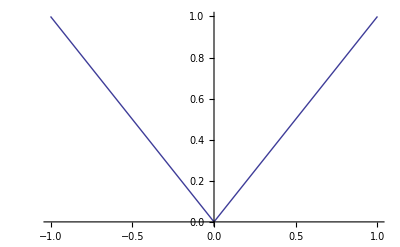

```mathematica
Plot[abspw[x],{x,-1,1}]
```

```mathematica
Clear[abs];
abs[x_]:=x/;x≥0;
abs[x_]:=-x/;x<0
```

```mathematica
Integrate[abs[x],{x,-1,1}]
```

∫_-1^1 abs[x]ⅆx

```mathematica
N[Integrate[abs[x],{x,-1,1}]]
```

1.

```mathematica
D[abs[x],x]
```

abs'[x]

```mathematica
Clear[fact];
fact[0]=1;
fact[n_]:=If[IntegerQ[n]&&n>0,n fact[n-1]];
{fact[5],fact[-3],fact[2.4]}
```

{120,Null,Null}

```mathematica
fact::noinit="Argument `1` is not a positive integer.";
fact[n_]:=If[IntegerQ[n]&&n>0,n fact[n-1],Message[fact::noinit,n]]
```

```mathematica
fact[-3]
```

fact::noinit: Argument -3 is not a positive integer.

```mathematica
fact1[0]=1;
fact1[n_]:=n fact[n-1]/;IntegerQ[n]&&n>0
```

```mathematica
{fact1[5],fact1[-3],fact1[2.4]}
```

{120,fact1[-3],fact1[2.4]}

```mathematica
fact2[0]=1;
fact2[n_/;IntegerQ[n]&&n>0]:=n fact2[n-1]
```

```mathematica
{fact2[5],fact2[-3],fact2[2.4]}
```

{120,fact2[-3],fact2[2.4]}

```mathematica
fact3[0]=1;
fact3[n_?IntegerQ/;n>0]:=n fact3[n-1]
```

```mathematica
{fact3[5],fact3[-3],fact3[2.4]}
```

{120,fact3[-3],fact3[2.4]}